Following http://matt.might.net/articles/counting-hash-collisions/

Let d=2^K be the number of different hashes. Now sample, with replacement, n randomly chosen hashes. The first hash doesn’t collide with any other. Its prob of not colliding is 1; prob of colliding is 0. The second hash has a chance of not colliding equal to (d-1)/d. The third has a chance of not colliding with any of the other two of ((d-1)/d)^2. After k hashes, the chance of having no collisions at all is ((d-1)/d)^(k-1); the chance that the k^th arrival collides with exactly one of the earlier arrivals is 1-((d-1)/d)^(k-1). The expected number of collisions is the number of collisions added by the first arrival, plus the additional collisions added by the second arrival, ..., up to the additional collisions added by the n-th arrival.

```mathematica
Module[{d},(   Sum[1-((d-1)/d)^(k-1),{k,1,n}]  ==   n+d(((d-1)/d)^n-1)   ==   (n-d+d(1-1/d)^n)   )//FullSimplify]
```

True

```mathematica
(n+d(((d-1)/d)^n-1))/.{d->2^128,n->2}
```

1/340282366920938463463374607431768211456

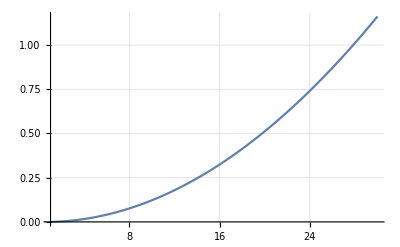

```mathematica
Plot[(n+d(((d-1)/d)^n-1))/.{d->365},{n,1,30},GridLines->Automatic]
```

```mathematica
Manipulate[
Plot[(n+d(((d-1)/d)^n-1))/.{d->2^k},{n,1,5},
GridLines->Automatic],
{{k,16},1,256,1}]
```

```mathematica
Manipulate[
Table[N@(n+d(((d-1)/d)^n-1))/.{d->2^k},{n,1,51,10}],
{{k,16},1,256,1}]
```